Emerging strategies of adversarial AIs for Tic-Tac-Toe & 2048
by Wolfram Emerging Leaders Program

## Abstract

Artificial Intelligences, also known as AIs, are the current coding system on the market. They're being used in countless fields for countless purposes, but with the emergence of more AIs comes an important question. What would happen if two AIs were paired against each other? What strategies would the AIs come up with to win against each other? The goal of our project was to answer this question. Starting with the simple game of Tic-Tac-Toe, we found unique strategies that the AIs developed; we later branched into more complex games such as 2048.

## Tic-Tac-Toe: Building an AI

We first decided to explore adversarial pair AIs with the simple game of Tic-Tac-Toe. The game has been studied many times, and is relatively simple to code as well, so it was a great choice to begin our project.

### Setting up the Game

Before we could build an AI, we had to set up code to play the game. We intended to use 0's for spots that weren't filled, 1's for spots that were filled by player 1, and 2's for spots that were filled by player 2. We started off with a 2D table to keep track of the board's current state.

startingboard kept track of the game board's current state:

```mathematica
startingboard = Table[{0,0,0}, 3];
```

We then set up functions to look at the board and figure out which player won. To do this, we set up functions to check the columns, rows, and diagonals, then combined it all in one function.

Column, Row, and Diagonal functions:

```mathematica
column[list_]:=Table[Equal@@list[[All,column]],{column,1,3}]
row[list_]:=Table[Equal@@list[[row,All]],{row,1,3}]
diagonal[list_]:={Equal@@{list[[1,1]],list[[2,2]],list[[3,3]]},Equal@@{list[[1,3]],list[[2,2]],list[[3,1]]}}
```

Our final win function, called actualWinner, used the column, row, and diagonal check functions to see who won. If the function returned 0, that meant neither player won and the game should continue.

Function to check for the final winner:

```mathematica
winnerRCD[list_]:=First[First[Position[Flatten@{column[list],row[list],diagonal[list]},True],{9}]]

actualWinner[list_]:=Which[winnerRCD[list]≤3,list[[1,winnerRCD[list]]],
winnerRCD[list]≤6, list[[Floor[winnerRCD[list]/3],1]],winnerRCD[list]≤8,list[[2,2]],True,0]
```

We then created a function that checked if all the spots on the board were filled. Combined with the win function, this checked for draws, where neither player won.

```mathematica
gameOver2[tictactoe_]:=!MemberQ[Flatten[tictactoe],0]
```

Finally, we wrote code that found a random empty space on the board for the player to use, and combined it with a function that replaced the spot with the player's number, 1 or 2.

Code to choose an empty spot on the board and "play" a turn:

```mathematica
playturnPosition[List_]:=Module[{board=Flatten[List], positions = Flatten[Position[Flatten[List], 0]]},  
If[gameOver2[List],"Game Over",RandomChoice[positions]]]

simulate1Move[boardWhat_, randomPosition_,playerNumber_]:= Module[{startingboard = boardWhat},
startingboard[[(Floor[(randomPosition-1)/3]+1),(randomPosition-(3*(Floor[(randomPosition-1)/3])))]] =playerNumber;
startingboard]
```

For example, given the starting board, the resulting tic-tac-toe board after player 1 moves is:

```mathematica
simulate1Move[startingboard,playturnPosition[startingboard],1]
```

{{0,0,0},{0,0,0},{0,1,0}}

where playturnPosition[startingboard] returns a random empty position for player 1 to move to.

### Creating Training Sets

To set up our AIs, they needed training sets to learn from. We built these training sets from running thousands of random games and every time someone won, we added the list of boards to their dataset. Over time, this accumulated into many example games that each player won.

We first set up training sets for our two AIs.

Training Sets for our two AIs:

```mathematica
AI1 = {};
AI2 = {};
```

Before we could fill the training sets, however, we needed to have code that could simulate tic-tac-toe games, so we combined all the functions we wrote above into one massive function, which played random tic-tac-toe games a certain number of times.

Function that simulates a given number of random tic-tac-toe games, and adds the list of boards to the winning player's dataset:

```mathematica
runSoManyEveryTimes[repeat_]:= 
Table[
startingboard=Table[{0,0,0},3];
firstplayer = 1;
listOfgrids = {startingboard};
While[!gameOver2[startingboard]&&!(actualWinner[startingboard]≠0),
startingboard=simulate1Move[startingboard,playturnPosition[startingboard],firstplayer];
listOfgrids=Append[listOfgrids,startingboard];
firstplayer = If[EvenQ[(firstplayer+1)],2,1];
];
If[actualWinner[startingboard]==1,AI1 = Append[AI1, AssociationThread[listOfgrids,RotateLeft[listOfgrids,1]][[Range[(Length@listOfgrids)/2]*2-1]]],
If[actualWinner[startingboard]==2,AI2 = Append[AI2, AssociationThread[listOfgrids,RotateLeft[listOfgrids,1]][[Range[Floor[(Length@listOfgrids)/2]]*2]]];
]],{n,1,repeat}]
```

We then ran 30,000 random games and put the training data in an association. The reason we put it in an association was so we could connect a certain current board to the next logical move, making it easier later to build an actively learning AI.

```mathematica
runSoManyEveryTimes[30000];
trainingData1=Merge[AI1,List];
trainingData2=Merge[AI2,List];
```

Here's some basic info about the training data, including the wins for player 1, the wins for player 2, and the amount of draws.

```mathematica
{Length@AI1, Length@AI2, 30000- Length@AI1 - Length@AI2}
```

{16574,10471,2955}

Here's an example of a winning game for player 1:

```mathematica
AI1[[14789]]
```

<|{{0,0,0},{0,0,0},{0,0,0}}→{{0,0,0},{1,0,0},{0,0,0}},{{0,0,0},{1,2,0},{0,0,0}}→{{0,0,0},{1,2,0},{0,0,1}},{{0,0,0},{1,2,2},{0,0,1}}→{{0,1,0},{1,2,2},{0,0,1}},{{2,1,0},{1,2,2},{0,0,1}}→{{2,1,0},{1,2,2},{1,0,1}},{{2,1,2},{1,2,2},{1,0,1}}→{{2,1,2},{1,2,2},{1,1,1}}|>

where player 1 wins by taking the diagonal and selecting the center spot.

### Actively Learning

So far, we have AI1, a list of winning boards for player 1, and AI2, a list of winning boards for player 2. The variable trainingData nicely puts this information in an association.

To use this information to play, the AIs check what they have in their trainingData. If the tic-tac-toe board exists, the player chooses one of the options in its dataset. If the tic-tac-toe board doesn't exist, the player just moves randomly.

For a significant number of training games in a player's dataset (these are random games), the training data for player 1 looks something like this:

```mathematica
Dataset[Counts[Normal@trainingData1]]//ReverseSort
```

-Graphics-

Our next step was to create a function that uses the training data for each player to predict the next move. The games that player 1 wins by using its dataset are stored in goodgame1, and the games that player 2 wins, using its dataset, are stored in goodgame2.

Setting up goodgame1 and goodgame2:

```mathematica
goodgame1 = {};
goodgame2 = {};
```

The function that uses the training data to play is shown below. Note that the training data for each player gets updated after each game, which is how the AIs actively learn.

Function that simulates a given amount of games using the AIs training data:

```mathematica
runUsingDataSet[repeat_]:=
Module[{},Table[
startingboard=Table[{0,0,0},3];
firstplayer = 1;
listOfgrids = {startingboard};
While[!gameOver2[startingboard]&&!(actualWinner[startingboard]≠0),
Which[firstplayer==1,If[Length@KeyTake[trainingData1,{startingboard}]≠0,startingboard = RandomChoice@Flatten[Values@KeyTake[trainingData1,{startingboard}],2],startingboard=simulate1Move[startingboard,playturnPosition[startingboard],firstplayer]],
firstplayer==2, If[Length@KeyTake[trainingData2,{startingboard}]≠0,startingboard = RandomChoice@Flatten[Values@KeyTake[trainingData2,{startingboard}],2],startingboard=simulate1Move[startingboard,playturnPosition[startingboard],firstplayer]]];
listOfgrids=Append[listOfgrids,startingboard];
firstplayer = If[EvenQ[(firstplayer+1)],2,1];
];

If[actualWinner[startingboard]==1,goodgame1 = Append[goodgame1, listOfgrids],If[actualWinner[startingboard]==2,goodgame2 = Append[goodgame2, listOfgrids];]];
If[actualWinner[startingboard]==1,AI1 = Append[AI1, AssociationThread[listOfgrids,RotateLeft[listOfgrids,1]][[Range[(Length@listOfgrids)/2]*2-1]]],If[actualWinner[startingboard]==2,AI2 = Append[AI2, AssociationThread[listOfgrids,RotateLeft[listOfgrids,1]][[Range[Floor[(Length@listOfgrids)/2]]*2]]];]];

trainingData1 = Merge[AI1,List];
trainingData2 = Merge[AI2,List];
,{n,1,repeat}]]
```

After running 10 games with the dataset, here's a look at the stats for each player.

```mathematica
runUsingDataSet[10];
Length@goodgame1
```

4

```mathematica
Length@goodgame2
```

6

Here's a game where player 1 wins (through the center column):

```mathematica
Grid/@goodgame1[[2]]
```

{0 | 0 | 0
0 | 0 | 0
0 | 0 | 0,0 | 0 | 0
0 | 0 | 1
0 | 0 | 0,0 | 0 | 0
0 | 0 | 1
0 | 0 | 2,0 | 0 | 0
0 | 1 | 1
0 | 0 | 2,0 | 0 | 0
0 | 1 | 1
2 | 0 | 2,1 | 0 | 0
0 | 1 | 1
2 | 0 | 2,1 | 0 | 0
2 | 1 | 1
2 | 0 | 2,1 | 0 | 0
2 | 1 | 1
2 | 1 | 2,1 | 0 | 2
2 | 1 | 1
2 | 1 | 2,1 | 1 | 2
2 | 1 | 1
2 | 1 | 2}

Here's a game where player 2 wins (through the center column):

```mathematica
Grid/@goodgame2[[2]]
```

{0 | 0 | 0
0 | 0 | 0
0 | 0 | 0,0 | 0 | 0
0 | 0 | 0
0 | 0 | 1,0 | 2 | 0
0 | 0 | 0
0 | 0 | 1,0 | 2 | 0
0 | 0 | 1
0 | 0 | 1,0 | 2 | 0
0 | 0 | 1
0 | 2 | 1,1 | 2 | 0
0 | 0 | 1
0 | 2 | 1,1 | 2 | 0
0 | 2 | 1
0 | 2 | 1}

Finally, we can combine all these functions into one final function that has two AIs play against each other in a game of tic-tac-toe.

Final tic-tac-toe function for adversarial pair AIs, that first plays a certain number of random games, and then plays a certain number of actual games using the players' datasets:

```mathematica
playTicTacToe[random_,actual_]:=Module[{},
AI1={};
AI2 = {};
runSoManyEveryTimes[random];
trainingData1 = Merge[AI1,List];
trainingData2 = Merge[AI2,List];
goodgame1 = {};
goodgame2 = {};
runUsingDataSet[actual]
]
```

## Tic-Tac-Toe: Analyzing Adversarial Pair AIs

We wrote code to build 2 AIs for tic-tac-toe and have them play against each other. Now, we need to analyze it. How do the AIs win? What strategies do they come up with? Over time, does a certain AI win or do the games end in ties?

### Strategies

We started off by analyzing the AIs first moves, to see if it differed from the conventional concept of choosing the center piece. For player 1, it appeared that the top left corner was the most commonly picked spot for the first move.

```mathematica
Counts@Flatten[Values[KeyTake[trainingData1,{{{0,0,0},{0,0,0},{0,0,0}}}]],2]
```

<|{{0,0,0},{0,0,0},{0,1,0}}→3116,{{1,0,0},{0,0,0},{0,0,0}}→4758,{{0,0,0},{0,1,0},{0,0,0}}→3861,{{0,0,0},{0,0,1},{0,0,0}}→2906,{{0,0,1},{0,0,0},{0,0,0}}→3947,{{0,1,0},{0,0,0},{0,0,0}}→3544,{{0,0,0},{1,0,0},{0,0,0}}→4090,{{0,0,0},{0,0,0},{1,0,0}}→3457,{{0,0,0},{0,0,0},{0,0,1}}→3534|>

For player 2, it appeared that when player 1 picked the top left corner, it selected the spot below that— the center left spot. It did pick the center spot as the 2nd most common location, though.

```mathematica
Counts@Flatten[Values[KeyTake[trainingData2,{{{1,0,0},{0,0,0},{0,0,0}}}]],2]
```

<|{{1,0,0},{0,0,0},{0,2,0}}→88,{{1,0,0},{0,0,2},{0,0,0}}→147,{{1,0,0},{0,2,0},{0,0,0}}→257,{{1,0,0},{0,0,0},{2,0,0}}→112,{{1,0,2},{0,0,0},{0,0,0}}→140,{{1,0,0},{0,0,0},{0,0,2}}→77,{{1,0,0},{2,0,0},{0,0,0}}→278,{{1,2,0},{0,0,0},{0,0,0}}→103|>

Clearly, the AI's first moves differ from what we expected.

### Graphs

To find the AI's winning patterns over time, we ran many random games and graphed the results.

To start off, we ran 100 random games for the AIs to learn from, and then played 100 real games to see how often player 1 won. The x-axis is the number of training games, while the y-axis is how many games were won.

```mathematica
listPlayer1Wins={};
Table[playTicTacToe[n,100];
listPlayer1Wins = Append[listPlayer1Wins,Length@goodgame1]
,{n,0,100,1}];
```

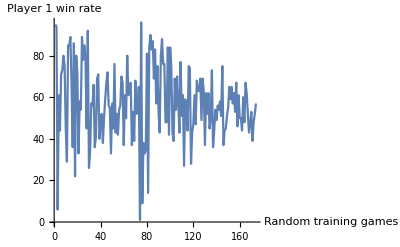

```mathematica
ListLinePlot[listPlayer1Wins,AxesLabel->{"Random training games", "Player 1 win rate"}]
```

As the AIs had more training data, their win rate started to even out. With only 20 random games for training data, it seems like player 1 won and lost quite randomly, but as more and more training data accumulated, player 1's win rate started to even out between 45% and 55%.

We then graphed the wins and losses of the AIs with even more training data— increments of 2,000 random games up to 30,000 random games. Again, the x-axis is the number of training games, while the y-axis is how many games were won.

```mathematica
listPlayer2Wins={};
listPlayer1Wins = {};
```

```mathematica
Table[playTicTacToe[n,100];
listPlayer2Wins = Append[listPlayer2Wins,Length@goodgame2];
listPlayer1Wins = Append[listPlayer1Wins,Length@goodgame1];
,{n,0,30000,2000}];
```

```mathematica
ListLinePlot[{listPlayer1Wins,listPlayer2Wins},AxesLabel->{"Random training games in increments of 2000", "Win Percentage"},PlotLabels->{"Player1","Player2"}]
```

Player 1 and 2's win rate similarly started to even out at 50%. We were unable to run more random games due to time constraints (our computers aren't supercomputers, unfortunately). If we were able to run, let's say up to 100,000 random games, we would like to see both players' win rate decrease to 0%, because when two humans play tic-tac-toe logically, it's a draw.

## Tic-Tac-Toe: Making an Interactive Game

After making these AIs, we decided to code it so that we could play against an AI— just to see who was smarter. We used a Manipulate and combined it with our two main functions from earlier: random games and training-based games.

We first created an interactive check box, where the humans can select where they want to move. The checkbox would influence the startingboard, which then would run the AI’s move and display the changes on the board. This went on until the game ended, either a draw or a win.

A challenge was timing player's 2 (the AI) moves, because the Manipulate updates constantly. We wanted to use something similar to a Wait function, where after AI moves, the human is given enough time to select a checkbox. For this, we used a Pause function, where the human is given 5 seconds to make a move. If the human doesn't make a move in 5 seconds, the AI just makes another move. 2 moves in a row, yay!

Here is an interactive tic-tac-toe game, where the AI moves RANDOMLY. Note that you'll have 5 seconds to make your move, and you'll need to wait a bit after your move, to give time for the AI to play.

```mathematica
startingBoard2=Table[{0,0,0},3];
Manipulate[Grid[Take[startingBoard2,3,3]],Dynamic[Panel[If[actualWinner[startingBoard2]≠1,(Grid[Outer[Checkbox[Dynamic[startingBoard2[[#1,#2]]],{0,1}]&,Range[3],Range[3]]]),"You Won"]]],SaveDefinitions->True]

Table[If[actualWinner[startingBoard2]≠1&&actualWinner[startingBoard2]≠2&&gameOver2[startingBoard2]≠True,Pause[5];startingBoard2=simulate1Move[startingBoard2,playturnPosition[startingBoard2],2]],{n,5}];Grid@startingBoard2
```

0 | 0 | 2
2 | 0 | 2
0 | 2 | 2

Here is the same interactive tic-tac-toe game where the AI uses it's dataset and makes logical moves. See the difference?

This is with the AI as player 2, so you go first:

```mathematica
startingBoard3=Table[{0,0,0},3];
(*with dataset*)
Manipulate[Grid[Take[startingBoard3,3,3]],Dynamic[Panel[If[actualWinner[startingBoard3]≠1 &&actualWinner[startingBoard3]≠2&&gameOver2[startingBoard3]≠True,(Grid[Outer[Checkbox[Dynamic[startingBoard3[[#1,#2]]],{0,1}]&,Range[3],Range[3]]]),"Game Over, figure out who won :)"]]],SaveDefinitions->True]

Table[If[actualWinner[startingBoard3]≠1&&actualWinner[startingBoard3]≠2&&gameOver2[startingBoard3]≠True,Pause[5];

If[Length@KeyTake[trainingData2,{startingBoard3}]≠0,startingBoard3 = RandomChoice@Flatten[Values@KeyTake[trainingData2,{startingBoard3}],2] (*using dataset*),startingBoard3=simulate1Move[startingBoard3,playturnPosition[startingBoard3],2]]],{n,5}];Grid@startingBoard3
```

0 | 2 | 2
2 | 0 | 2
0 | 2 | 0

This is with the AI as player 1, so you go second:

```mathematica
startingBoard4=Table[{0,0,0},3];
(*with dataset*)
Manipulate[Grid[Take[startingBoard4,3,3]],Dynamic[Panel[If[actualWinner[startingBoard4]≠1 &&actualWinner[startingBoard4]≠2&&gameOver2[startingBoard4]≠True,(Grid[Outer[Checkbox[Dynamic[startingBoard4[[#1,#2]]],{0,2}]&,Range[3],Range[3]]]),"Game Over, figure out who won :)"]]],SaveDefinitions->True]

Table[If[actualWinner[startingBoard4]≠1&&actualWinner[startingBoard4]≠2&&gameOver2[startingBoard4]≠True,Pause[5];

If[Length@KeyTake[trainingData1,{startingBoard4}]≠0,startingBoard4 = RandomChoice@Flatten[Values@KeyTake[trainingData1,{startingBoard4}],2] (*using dataset*),startingBoard4=simulate1Move[startingBoard4,playturnPosition[startingBoard4],1]]],{n,5}];Grid@startingBoard2
```

0 | 0 | 2
2 | 0 | 2
0 | 2 | 2

The manipulate is fantastic!!! Enjoy playing tic-tac-toe.

Note that the manipulate works a lot better with 120,000 random training games, rather than 30,000 games.

## 2048: Building an AI

2048 is a popular game, where the the goal is to add powers of 2 on a 4 by 4 grid. The human wins when the sum of one square reaches 2048.

2048 and tic-tac-toe are massively different games, especially when it comes to the composition of the game:
2048 is a single player game, whereas tic-tac-toe is a two player game. Due to this, we could not take the adversarial pair approach. 2048 has many, many more possible board combinations. Tic-tac-toe has a 3 by 3 grid, with each slot either being and X, O, or empty. 2048 is a 4 by 4 board, with each slot being a 2, 4, 8, 16, 32, 64, 128, 256, 512, 1024, 2048, or empty. This means that the board reference strategy would also be ineffective, and would ultimately be more difficult to build an AI around.

The overall strategy was to first construct the game, and then generate a large set of random games to train a random forest model on. Then we compared statistics between the datasets.

### Setting up the Game

Similarly to how we built a model for tic-tac-toe, the first step in testing AI on 2048 is building the game. In the game, zeros represent empty spaces, and all other numbers are self-explanatory blocks on the board.

A simple function to build a starting board by making a 4 by 4 table, and populating it with the random starting numbers in random positions— the goal is to produce a different board each time:

```mathematica
InitializeBoard[] :=Module[{idx1,idx2,val,boardlocal},boardlocal=Table[{0,0,0,0},4];
Do[
idx1=RandomInteger[{1,4}];
idx2=RandomInteger[{1,4}];
If[RandomReal[]<0.9, val = 2, val=4];
 boardlocal[[idx1]][[idx2]]=val,2];
Return[boardlocal]
]
```

The next step is to build the functionality of the game. This means writing a function for each of the 4 possible moves (up, down, left, and right), one to check if the game is over, and a driver to combine all of them to play a game.

The first 2 move functions operate similarly, systematically checking for any possible moves or combinations in the desired direction of moving left or right:

```mathematica
MoveRight[board_]:=Module[{boardlocal=board,poszeros,posswap,posmerge,val},
Do[
Do[If[boardlocal[[row]][[pos]]≠ 0,
poszeros=Flatten[Position[boardlocal[[row]],0],1];
posswap=Max[Select[poszeros,#>pos&]];
If[posswap>0&&posswap<Infinity,
boardlocal[[row]][[posswap]]=boardlocal[[row]][[pos]];
boardlocal[[row]][[pos]]=0;
posmerge=posswap,
posmerge=pos
];
If[posmerge<4,
If[boardlocal[[row]][[posmerge]]==boardlocal[[row]][[posmerge+1]],
boardlocal[[row]][[posmerge+1]]=boardlocal[[row]][[posmerge+1]]*2;
boardlocal[[row]][[posmerge]]=0;
]
]
]
,{pos,{3,2,1}}]
,{row,4}
];
poszeros=Position[boardlocal,0];
If[Length[poszeros]>0,
posswap=poszeros[[RandomInteger[{1,Length[poszeros]}]]];
If[RandomReal[]<0.9, val = 2, val=4];
boardlocal[[posswap[[1]]]][[posswap[[2]]]]=val;
];
Return[boardlocal]
]
```

```mathematica
MoveLeft[board_]:=Module[{boardlocal=board,poszeros,posswap,posmerge,val},
Do[
Do[If[boardlocal[[row]][[pos]]≠ 0,
poszeros=Flatten[Position[boardlocal[[row]],0],1];
posswap=Min[Select[poszeros,#<pos&]];

If[posswap>0&&posswap<Infinity,
boardlocal[[row]][[posswap]]=boardlocal[[row]][[pos]];
boardlocal[[row]][[pos]]=0;
posmerge=posswap,
posmerge=pos
];
If[posmerge>1,
If[boardlocal[[row]][[posmerge]]==boardlocal[[row]][[posmerge-1]],
boardlocal[[row]][[posmerge-1]]=boardlocal[[row]][[posmerge-1]]*2;
boardlocal[[row]][[posmerge]]=0;
]
]
]
,{pos,{2,3,4}}]
,{row,4}
];
poszeros=Position[boardlocal,0];
If[Length[poszeros]>0,
posswap=poszeros[[RandomInteger[{1,Length[poszeros]}]]];
If[RandomReal[]<0.9, val = 2, val=4];
boardlocal[[posswap[[1]]]][[posswap[[2]]]]=val;
];

Return[boardlocal]
]
```

The next two possible moves, up and down, are a lot simpler— the board is simply transposed:

```mathematica
MoveUp[board_]:=
Module[{boardlocal},
boardlocal=Transpose[MoveLeft[Transpose[board]]];
Return[boardlocal]
]
```

```mathematica
MoveDown[board_]:=
Module[{boardlocal},
boardlocal=Transpose[MoveRight[Transpose[board]]];
Return[boardlocal]
]
```

The game end check just looks to see if there are either no available merges or moves, or if the goal of 2048 has been achieved, and returns a corresponding True or False:

```mathematica
GameEndCheck[board_]:=Module[{zeros,movefound,transposedboard,objective,objectivefound},
zeros=Position[board,0];
objective=Position[board,2048];
transposedboard=Transpose[board];
If[Length[zeros]>0,movefound=True,movefound=False];
If[Length[objective]>0,Return[True]];
While[movefound==False,
Do[
Do[If[board[[row]][[pos]]==board[[row]][[pos-1]]||board[[row]][[pos]]==board[[row]][[pos+1]],movefound=True]
,{pos,{2,3}}
]
,{row,4}
];
Do[
Do[If[transposedboard[[row]][[pos]]==transposedboard[[row]][[pos-1]]||transposedboard[[row]][[pos]]==transposedboard[[row]][[pos+1]],movefound=True]
,{pos,{2,3}}
]
,{row,4}
];
Break[]
];
If[movefound==False,Return[True],Return[False]]
]
```

The game driver went through several iterations over the course of this project. The first implementation used a user interface to allow a human to play a game in the notebook, and was used for debugging the game code. The second version made random moves until the game was over (either succeeded or no possible moves remained), and was used to generate a large dataset of games. The final version used a trained ML model (through the Predict function) to decide the next move. While testing this last one, we ran into a problem: occasionally the model would select a move that doesn’t end up changing the board, resulting in an endless loop. To fix this, we implemented a simple detection statement to see if the board has changed in the past couple moves, and if it has not changed, it uses a random move instead of the move predicted by the model.

Model 1— a user interface to debug the game code:

```mathematica
RunGame[]:=Module[{board,movelist,gameover=False,move,checkend},
board=InitializeBoard[];
Print[TableForm[board]];
While[gameover==False,
move=InputString["Move: L, R, U, D, or Q"];
If[move=="L",board=MoveLeft[board]];
If[move=="R",board=MoveRight[board]];
If[move=="U",board=MoveUp[board]];
If[move=="D",board=MoveDown[board]];
If[move=="Q",gameover=True];
Print[TableForm[board]];
checkend=GameEndCheck[board];
If[checkend!=0,gameover=True];
];
If[checkend==2,Print["success"],Print["fail"]]

]
```

Model 2— running random games to create a large dataset:

```mathematica
RunRandomGame[]:=Module[{board,movelist,gameover=False,move,checkend},
board=InitializeBoard[];
movelist={};
While[gameover==False,
move=RandomInteger[{1,4}];
AppendTo[movelist,{board,move}];
If[move==1,board=MoveLeft[board]];
If[move==2,board=MoveRight[board]];
If[move==3,board=MoveUp[board]];
If[move==4,board=MoveDown[board]];
If[move=="Q",gameover=True];
checkend=GameEndCheck[board];
If[checkend!=0,gameover=True];
];
If[checkend==2,AppendTo[movelist,"success"],AppendTo[movelist,"fail"]];
Return[movelist]

]
```

Model 3— a trained ML model to decide the next move:

```mathematica
RunModelGame[]:=Module[{board,movelist,gameover=False,move,checkend},
board=InitializeBoard[];
movelist={};
While[gameover==False,
move=PredictBestMove[board];
If[Length[movelist]>0,If[{board,move}==movelist[[-1]],move=RandomInteger[{1,4}]]];
AppendTo[movelist,{board,move}];
If[move==1,board=MoveLeft[board]];
If[move==2,board=MoveRight[board]];
If[move==3,board=MoveUp[board]];
If[move==4,board=MoveDown[board]];
If[Length[Position[board,0]]==0,gameover=GameEndCheck[board],gameover=False];
];
If[checkend==2,AppendTo[movelist,"success"],AppendTo[movelist,"fail"]];
Return[movelist]

]
```

### Gathering Data and Building a Model

The next step in the process was building a large enough dataset of random games to train a predict function on. We ran 70,000 games overnight, which seemed like a large enough dataset.

The first step was to compose a function to play a number of games and save that to a variable:

```mathematica
PlayXGames[games_]:=Module[{dataset},
dataset={};
Do[AppendTo[dataset,RunRandomGame[]],games];
Return[dataset]
]
```

```mathematica
data=PlayXGames[70000];
```

We exported this to make it easier to save and work with.

After generating the data and looking at it, we realized that none of them achieved the goal of 2048, and so the fail or success statements at the end were unnecessary. Furthermore, the strings at the end of the game, “fail” or “success”, made the numerical data hard to work with. To fix that, we wrote some code that cuts off the last element of each game (the result statement).

Code to cut off the result statement:

```mathematica
MyDrop[list_]:= Return[Drop[list,-1]]
data2 = MyDrop /@ data;
```

We ran the steps shown above to create data2, and then exported this to the cloud. Below you can see the CloudImport method, which is much quicker than running 70,000 random games.

```mathematica
data2=CloudImport["https://www.wolframcloud.com/obj/1f0dab02-fe9f-400e-84f2-8516515fdbd7"]
```

{{{{{0,0,0,0},{2,0,0,2},{0,0,0,0},{0,0,0,0}},3},{{{2,0,0,2},{0,0,0,0},{0,2,0,0},{0,0,0,0}},2},{{{0,0,0,4},{0,0,0,0},{2,0,0,2},{0,0,0,0}},1},{{{4,0,0,0},{0,0,0,0},{4,0,0,2},{0,0,0,0}},2},{{{0,2,0,4},{0,0,0,0},{0,0,4,2},{0,0,0,0}},2},{{{0,0,2,4},{0,2,0,0},{0,0,4,2},{0,0,0,0}},4},{{{0,0,0,0},{0,0,0,0},{2,0,2,4},{0,2,4,2}},3},{{{2,2,2,4},{0,0,4,2},{0,0,0,0},{0,4,0,0}},2},99,{{{2,8,2,2},{8,64,4,0},{16,4,16,8},{4,32,64,4}},2},{{{0,2,8,4},{4,8,64,4},{16,4,16,8},{4,32,64,4}},3},{{{4,2,8,16},{16,8,64,4},{4,4,16,0},{0,32,64,2}},2},{{{4,2,8,16},{16,8,64,4},{2,0,8,16},{0,32,64,2}},2},{{{4,2,8,16},{16,8,64,4},{2,2,8,16},{0,32,64,2}},2},{{{4,2,8,16},{16,8,64,4},{2,4,8,16},{0,32,64,2}},2},{{{4,2,8,16},{16,8,64,4},{2,4,8,16},{2,32,64,2}},4},{{{2,2,8,16},{4,8,64,4},{16,4,8,16},{4,32,64,2}},2}},69998,{{{1},3},82}}
 |  |  |  |

We then needed to reformat the data so that it could be used by the Predict function.

A function that formats the data into a list of rules, as needed by the Predict:

```mathematica
trainingset1={};

rndData = data2;
rndmaxvalues=Map[Max,Map[Max,rndData,{2}],{1}];

For[i=1,i<70000,i++,{
a=#->rndmaxvalues[[i]]&/@Map[Flatten,data2[[i]]],
AppendTo[trainingset1,Flatten[a,2]]}]

trainingset2 = Flatten[trainingset1];
```

The final step was to train the Predict function and export it:

```mathematica
predictorV3 = Predict[trainingset2, Method->"RandomForest"];
```

After exporting the Predict function, we wrote code that combined it with our game. We built a function that takes the current board passed in, and runs each possible move. It uses the model to predict the highest score of each possible move, and then uses that move.

Function to predict the best next move:

```mathematica
PredictBestMove[board_]:=Module[{newboard,bestmove={},newscore},
For[i=1,i<=4,i++, {
newboard=Flatten[board];
AppendTo[newboard,i];
newscore=predictorV3[newboard];
If[i==1,AppendTo[bestmove,{newscore,i}],
If[newscore>bestmove[[1]][[1]],bestmove={{newscore,i}},
If[newscore==bestmove[[1]][[1]],AppendTo[bestmove,{newscore,i}]]]]}];
Return[RandomSample[bestmove,1][[1]][[2]]]
```

Function to play a large number of games:

```mathematica
PlayXModelGames[games_]:=Module[{dataset},
dataset={};
Do[AppendTo[dataset,RunModelGame[]],games];
Return[dataset]]
```

These games ran more slowly, running over the course of 2 nights. We've imported it from the cloud, to make it easier.

```mathematica
mdlData = CloudImport["https://www.wolframcloud.com/obj/db5dfdc0-f2a1-42c9-bc98-4a6da0e8258f"]
```

But, ultimately, it provides the same result as running this:

```mathematica
PlayXModelGames[50000];
```

## 2048: Analyzing the Model

The next step was to ask the logical question: did anything change from the expected results? We took some data from the sets and graphed them to see what happened. Note that rndData is the random data, while mdlData is the model data.

Identify the max value of each game in the sets:

```mathematica
rndmaxvalues=Map[Max,Map[Max,rndData,{2}],{1}];
mdlmaxvalues=Map[Max,Map[Max,mdlData,{2}],{1}];
```

Find the first occurrence of the maximum value:

```mathematica
PosMaxValue[list_]:= Return[First[Position[Map[Max,list,{1}],Max[Map[Max,list,{1}]]]][[1]]]
```

Extract the lengths of each game:

```mathematica
rndlengths=Map[Length,rndData,{1}];
mdllength=Map[Length,mdlData,{1}];
```

The next step is to make pairs of the maximum value and the length of each game in order to graph them against each other:

```mathematica
rndmaxlengthpairs=Thread[{rndlengths,rndmaxvalues}];
mdlmaxlengthpairs=Thread[{mdllength,mdlmaxvalues}];
```

We used this on both datasets— the random games, and the model games that use the Predict function:

```mathematica
rndposmaxvalues=Map[PosMaxValue,rndData,{1}];
mdlposmaxvalues=Map[PosMaxValue,mdlData,{1}];
```

Threading these results with the max values themselves:

```mathematica
rndmaxvalpairs=Thread[{rndposmaxvalues,rndmaxvalues}];
mdlmaxvalpairs=Thread[{mdlposmaxvalues,mdlmaxvalues}];
```

Here is the histogram of the lengths of each game in the datasets, with the yellow representing the random move data, the blue representing the model data, and the gray representing the overlapping regions. The x axis is the length of the game, and the y-axis is the amount of games with that length.

Distribution of the game lengths:

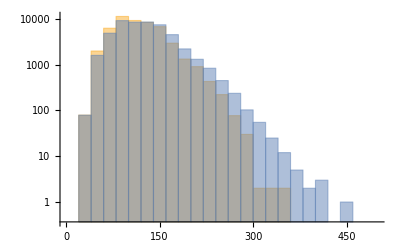

```mathematica
Histogram[{rndlengths,mdllength},{0,500,20},ScalingFunctions->{None,"Log"}]
```

Keep in mind the y-axis log scale! There are 10,000 times more games with length 100, than games with a length over 400.

As we can see, the model data (blue) has a longer tail than the random data (yellow), showing that games that use the dataset tend to run longer than random games. The yellow graph is skewed more to the right than the blue graph.

Here is the histogram of the maximum values with the same color code as the previous histogram. The x-axis represents the final value of the game (2, 4, 8, 16, etc, up to 512). There were no games that actually won (with a maximum value of 2048). The y-axis is the amount of games that achieved that final value. Most games ended at 64 and 128.  A significant portion of games that ended at 8 were a result of the random games.

Distribution of the maximum values in the game:

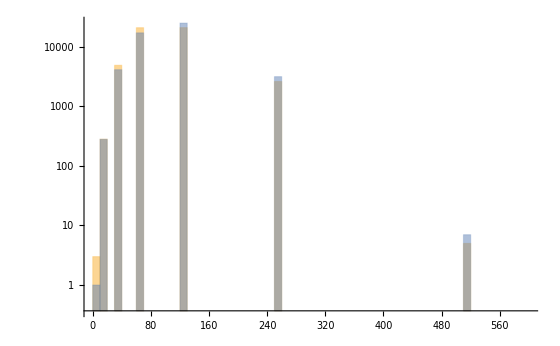

```mathematica
Histogram[{rndmaxvalues,mdlmaxvalues},{0,600,10},ScalingFunctions->{None,"Log"}]
```

In this plot, we can see that although there is some improvement of the number of the higher scores using the model,  it doesn’t appear to be significant in comparison to the random games.

Here we have the box and whisker plots of the lengths of the games, separated into bins based on the high score of the game, and the different datasets, using the same color code as above.

```mathematica
BoxWhiskerChart[{
{Flatten[Take[#,1]&/@Select[rndmaxlengthpairs,#[[2]]==8&]],
Flatten[Take[#,1]&/@Select[mdlmaxlengthpairs,#[[2]]==8&]]},
{Flatten[Take[#,1]&/@Select[rndmaxlengthpairs,#[[2]]==16&]],
Flatten[Take[#,1]&/@Select[mdlmaxlengthpairs,#[[2]]==16&]]},
{Flatten[Take[#,1]&/@Select[rndmaxlengthpairs,#[[2]]==32&]],
Flatten[Take[#,1]&/@Select[mdlmaxlengthpairs,#[[2]]==32&]]},
{Flatten[Take[#,1]&/@Select[rndmaxlengthpairs,#[[2]]==64&]],
Flatten[Take[#,1]&/@Select[mdlmaxlengthpairs,#[[2]]==64&]]},
{Flatten[Take[#,1]&/@Select[rndmaxlengthpairs,#[[2]]==128&]],
Flatten[Take[#,1]&/@Select[mdlmaxlengthpairs,#[[2]]==128&]]},
{Flatten[Take[#,1]&/@Select[rndmaxlengthpairs,#[[2]]==256&]],
Flatten[Take[#,1]&/@Select[mdlmaxlengthpairs,#[[2]]==256&]]},
{Flatten[Take[#,1]&/@Select[rndmaxlengthpairs,#[[2]]==512&]],
Flatten[Take[#,1]&/@Select[mdlmaxlengthpairs,#[[2]]==512&]]}
}
]
```

Bins are based on maximum scores (blue is model data, yellow is random data):

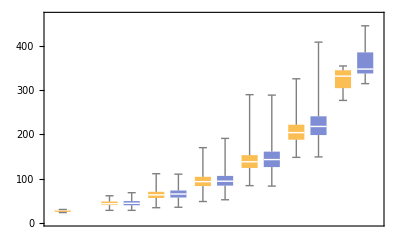

As we can see, each bin of games (e.g. max score of 8, 16, etc...) generally has very similar distributions whether the games are played randomly or using the Predict model, though the highest two bins (max scores of 256 and 512) show increased game lengths compared with the random move games.

The plot below uses the first occurrence of the max value rather than the length of the game.

```mathematica
BoxWhiskerChart[{
{Flatten[Take[#,1]&/@Select[rndmaxvalpairs,#[[2]]==8&]],
Flatten[Take[#,1]&/@Select[mdlmaxvalpairs,#[[2]]==8&]]},
{Flatten[Take[#,1]&/@Select[rndmaxvalpairs,#[[2]]==16&]],
Flatten[Take[#,1]&/@Select[mdlmaxvalpairs,#[[2]]==16&]]},
{Flatten[Take[#,1]&/@Select[rndmaxvalpairs,#[[2]]==32&]],
Flatten[Take[#,1]&/@Select[mdlmaxvalpairs,#[[2]]==32&]]},
{Flatten[Take[#,1]&/@Select[rndmaxvalpairs,#[[2]]==64&]],
Flatten[Take[#,1]&/@Select[mdlmaxvalpairs,#[[2]]==64&]]},
{Flatten[Take[#,1]&/@Select[rndmaxvalpairs,#[[2]]==128&]],
Flatten[Take[#,1]&/@Select[mdlmaxvalpairs,#[[2]]==128&]]},
{Flatten[Take[#,1]&/@Select[rndmaxvalpairs,#[[2]]==256&]],
Flatten[Take[#,1]&/@Select[mdlmaxvalpairs,#[[2]]==256&]]},
{Flatten[Take[#,1]&/@Select[rndmaxvalpairs,#[[2]]==512&]],
Flatten[Take[#,1]&/@Select[mdlmaxvalpairs,#[[2]]==512&]]}
}
]
```

First occurrence of the maximum values:

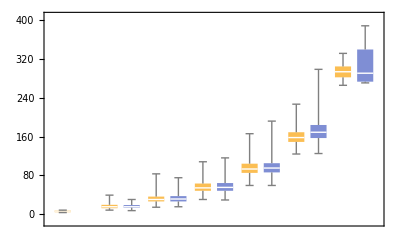

In this plot, we can see no real difference between the model-played and random move games, demonstrating that the model doesn’t lead to the games reaching their max value faster, as we had hypothesized.

As we can see from the graphs, the model learned how to increase the length of the games rather than bringing them to a higher score faster or more efficiently. This was an unforeseen outcome, but was still fascinating to observe.

The clear conclusion to this work is that the model using the RandomForest distribution made the games run longer, rather than more efficiently, despite being trained solely based on the high score of games. This makes sense, because as the games go on, the values never decrease, so a longer game will have a higher chance of getting a higher score.

## Conclusions and Future Work

We're very proud of our work!

We want to thank Rory for all their help throughout this project. We couldn't have accomplished this without them.

While our dataset approach for tic-tac-toe didn't use the Classify or Predict functions, it is still a unique approach that functions well in predicting the player's next logical move. This approach functions— given a good training dataset with a significant amount of winning games. We are curious how we could use those functions (Classify, Predict, LearnDistribution), however, to see whether the results would change for tic-tac-toe. The results of the training data can be seen in the manipulate, which makes logical moves most of the time! However, the manipulate was tricky to build in regards to giving enough time for the human to make a move. 

With the 2048, we would have liked to train the model directly on the game lengths rather than on the high scores, to see if it can more significantly increase the length of the played games. It would have also been interesting to see if with more data the AI could produce intelligent strategies as a human would, rather than just increasing the length of the games to increase the probability of getting a higher score (which is still logical!). It would also be interesting to see whether different neural net models, as opposed to the RandomForest model, would increase the accuracy. As opposed to using the Predict function, it may be less time-consuming to run each of the 4 possible moves (up, down, left, right), and take the board with the highest resulting value (using if-statements) for each move. The reason for including this would be as a control, to see if the machine learning model can outperform a simpler approach. 

Future work involves running a lot more random training games, so that neither player 1 nor player 2 wins (in tic-tac-toe if both players make logical moves it’s a draw, and in 2048 you actually reach the max value of 2048). It’d be great to apply this approach to more complex games as well, such as chess, Nim, or Scrabble. The hardest part is setting up the game—running the random training games and then using that dataset is shown how to do in this project.

To any intrigued readers, we wish you the best of luck in your future endeavours to further develop our work— if you and your computer are up to the challenge.